# Chaos Land.

## Linear homogeneous differential system with constant coefficients (r’=A.r), an example :

```mathematica
(* Example 1 : two dimensions *)  A={{1,-2},{0,1}}
```

{{1,-2},{0,1}}

```mathematica
A//MatrixForm
```

(1 | -2
0 | 1)

```mathematica
r[t]:={Subscript[x, 1][t],Subscript[x, 2][t]}
```

```mathematica
Thread[D[r[t],t]-A.r[t]==0]
```

{-x_1[t]+2 x_2[t]+x_1'[t]==0,-x_2[t]+x_2'[t]==0}

```mathematica
DSolve[Thread[D[r[t],t]-A.r[t]==0],{Subscript[x, 1],Subscript[x, 2]},t]
```

{{x_1→Function[{t},ⅇ^t C[1]-2 ⅇ^t t C[2]],x_2→Function[{t},ⅇ^t C[2]]}}

```mathematica
r[t_]:=MatrixExp[A t].{Subscript[x, 1][0],Subscript[x, 2][0]}
```

```mathematica
r[t]//MatrixForm
```

(ⅇ^t x_1[0]-2 ⅇ^t t x_2[0]
ⅇ^t x_2[0])

```mathematica
{D[r[t],t]-A.r[t]//Simplify,r[0]}
```

{{0,0},{x_1[0],x_2[0]}}

```mathematica
Clear[r];r[t_]:={Subscript[x, 1][t],Subscript[x, 2][t]};Inv[t_]:=MatrixExp[-A t].r[t]//Simplify
```

```mathematica
Inv[t]
```

{ⅇ^-t (x_1[t]+2 t x_2[t]),ⅇ^-t x_2[t]}

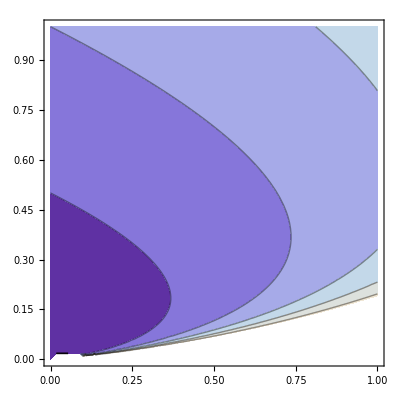

```mathematica
ContourPlot[x2 Exp[x1/(2x2)],{x1,0,1},{x2,0,1}]
```

```mathematica
D[Inv[t],t]//Simplify
```

{ⅇ^-t (-x_1[t]-2 (-1+t) x_2[t]+x_1'[t]+2 t x_2'[t]),ⅇ^-t (-x_2[t]+x_2'[t])}

```mathematica
(* Example 2 : three dimensions *)  A={{1,0,-2},{0,1,1},{1,1,3}}
```

{{1,0,-2},{0,1,1},{1,1,3}}

```mathematica
A//MatrixForm
```

(1 | 0 | -2
0 | 1 | 1
1 | 1 | 3)

```mathematica
MatrixExp[A t]//MatrixForm
```

(-ⅇ^t (1-2 ⅇ^t+2 ⅇ^t t) | -2 ⅇ^t (1-ⅇ^t+ⅇ^t t) | -2 ⅇ^(2 t) t
ⅇ^t (1-ⅇ^t+ⅇ^t t) | ⅇ^t (2-ⅇ^t+ⅇ^t t) | ⅇ^(2 t) t
ⅇ^(2 t) t | ⅇ^(2 t) t | ⅇ^(2 t) (1+t))

```mathematica
r[t_]:=MatrixExp[A t].{Subscript[x, 1][0],Subscript[x, 2][0],Subscript[x, 3][0]}
```

```mathematica
r[t]//MatrixForm
```

(-ⅇ^t (1-2 ⅇ^t+2 ⅇ^t t) x_1[0]-2 ⅇ^t (1-ⅇ^t+ⅇ^t t) x_2[0]-2 ⅇ^(2 t) t x_3[0]
ⅇ^t (1-ⅇ^t+ⅇ^t t) x_1[0]+ⅇ^t (2-ⅇ^t+ⅇ^t t) x_2[0]+ⅇ^(2 t) t x_3[0]
ⅇ^(2 t) t x_1[0]+ⅇ^(2 t) t x_2[0]+ⅇ^(2 t) (1+t) x_3[0])

```mathematica
{D[r[t],t]-A.r[t]//Simplify,r[0]}
```

{{0,0,0},{x0,y0,z0}}

```mathematica
Clear[r];r[t_]:={x[t],y[t],z[t]};Inv[t_]:=MatrixExp[-A t].r[t]//Simplify
```

```mathematica
D[Inv[t],t]//Simplify
```

{ⅇ^(-2 t) ((-2+ⅇ^t-4 t) x[t]+2 (-1+ⅇ^t-2 t) y[t]+2 z[t]-4 t z[t]+2 x'[t]-ⅇ^t x'[t]+2 t x'[t]+2 y'[t]-2 ⅇ^t y'[t]+2 t y'[t]+2 t z'[t]),-ⅇ^(-2 t) ((-1+ⅇ^t-2 t) x[t]+(-1+2 ⅇ^t-2 t) y[t]+z[t]-2 t z[t]+x'[t]-ⅇ^t x'[t]+t x'[t]+y'[t]-2 ⅇ^t y'[t]+t y'[t]+t z'[t]),2 ⅇ^(-2 t) (t x[t]+t y[t]+(-1+t) z[t])-ⅇ^(-2 t) (x[t]+y[t]+z[t]+t x'[t]+t y'[t]+(-1+t) z'[t])}

## Invariants of the 1D-harmonic oscillator

```mathematica
D[v[t]^2+ω^2 x[t]^2,t]/.{x'[t]->v[t],v'[t]->-ω^2 x[t]}
```

0

```mathematica
D[(Tan[ω t]-ω x[t]/v[t])/(1+ω x[t]/v[t] Tan[ω t]),t]/.{x'[t]->v[t],v'[t]->-ω^2 x[t]}//Simplify
```

0

## An artificial system (Third invariant)

```mathematica
sol=NDSolve[{x'[t]==x[t]z[t]-x[t]y[t],y'[t]==x[t]^2-x[t]z[t],z'[t]==x[t]y[t]-x[t]^2,x[0]==1,y[0]==2,z[0]==1},{x[t],y[t],z[t]},{t,0,5}]
ParametricPlot3D[Evaluate[{x[t],y[t],z[t]}/.sol,{t,0,5}],PlotStyle->Thick,LabelStyle->Directive[Large,Bold],AxesLabel->{x,y,z}]
```

{{x[t]→InterpolatingFunction[{{0.,5.}},<>][t],y[t]→InterpolatingFunction[{{0.,5.}},<>][t],z[t]→InterpolatingFunction[{{0.,5.}},<>][t]}}

-Graphics3D-

Checking the non obvious third invariant :

```mathematica
D[(((I1^2-2I2)-I1 x[t])Cos[t √(I1^2-2I2)]+(z[t]-y[t])√(I1^2-2I2)Sin[t √(I1^2-2I2)])/((z[t]-y[t])√(I1^2-2I2)Cos[t √(I1^2-2I2)]-((I1^2-2I2)-I1 x[t])Sin[t √(I1^2-2I2)]),t]/.{x'[t]->x[t]z[t]-x[t]y[t],y'[t]->x[t]^2-x[t]z[t],z'[t]->x[t]y[t]-x[t]^2}/.{I1->x[t]+y[t]+z[t],I2->x[t]^2+y[t]^2+z[t]^2}//FullSimplify
```

0

## Invariants of the 2D-Kepler problem (fixed center)

```mathematica
D[q[t],t]/.{r'[t]->p[t],θ'[t]->q[t]/r[t]^2,p'[t]->q[t]^2/r[t]^3-μ/r[t]^2,q'[t]->0}
```

0

```mathematica
D[q[t](p[t]Sin[θ[t]]+q[t]Cos[θ[t]]/r[t])-μ Cos[θ[t]],t]/.{r'[t]->p[t],θ'[t]->q[t]/r[t]^2,p'[t]->q[t]^2/r[t]^3-μ/r[t]^2,q'[t]->0}//Simplify
```

0

```mathematica
D[q[t](-p[t]Cos[θ[t]]+q[t]Sin[θ[t]]/r[t])-μ Sin[θ[t]],t]/.{r'[t]->p[t],θ'[t]->q[t]/r[t]^2,p'[t]->q[t]^2/r[t]^3-μ/r[t]^2,q'[t]->0}//Simplify
```

0

```mathematica
D[(((I2-μ)Tan[θ[t]/2]-I3)+I1 √(-2En)Tan[(I1 √(-2En)(I3 μ+(I2^2+I3^2)Sin[θ[t]]))/(2μ I2 (μ+I2 Cos[θ[t]]+I3 Sin[θ[t]]))-(En √(-2En)t)/μ])/(I1 √(-2En)-((I2-μ)Tan[θ[t]/2]-I3)Tan[(I1 √(-2En)(I3 μ+(I2^2+I3^2)Sin[θ[t]]))/(2μ I2 (μ+I2 Cos[θ[t]]+I3 Sin[θ[t]]))-(En √(-2En)t)/μ]),t]/.{θ'[t]->q[t]/r[t]^2,En->(I2^2+I3^2-μ^2)/(2I1^2)}/.{I1->q[t],I2->q[t](p[t]Sin[θ[t]]+q[t]Cos[θ[t]]/r[t])-μ Cos[θ[t]],I3->q[t](-p[t]Cos[θ[t]]+q[t]Sin[θ[t]]/r[t])-μ Sin[θ[t]]}//FullSimplify
```

0

## Third autonomous invariant of the 2D-harmonic oscillator

```mathematica
D[ω1 ArcTan[ω2 x2[t]/v2[t]]-ω2 ArcTan[ω1 x1[t]/v1[t]],t]/.{x1'[t]->v1[t],v1'[t]->-ω1^2 x1[t],x2'[t]->v2[t],v2'[t]->-ω2^2 x2[t]}//FullSimplify
```

0

```mathematica
m=3;n=2;Tan[m ArcTan[ω2 x2[t]/v2[t]]-n ArcTan[ω1 x1[t]/v1[t]]]/.{ω1->m ω,ω2->n ω}TrigExpand//FullSimplify
```

(-6 ω v1[t] v2[t]^3 x1[t]+6 ω v2[t]^2 (v1[t]^2-9 ω^2 x1[t]^2) x2[t]+72 ω^3 v1[t] v2[t] x1[t] x2[t]^2+8 ω^3 (-v1[t]^2+9 ω^2 x1[t]^2) x2[t]^3)/(v2[t]^3 (v1[t]^2-9 ω^2 x1[t]^2)+36 ω^2 v1[t] v2[t]^2 x1[t] x2[t]-12 ω^2 v2[t] (v1[t]^2-9 ω^2 x1[t]^2) x2[t]^2-48 ω^4 v1[t] x1[t] x2[t]^3)

Singlevaluedness of the former in the commensurable case, m=3, n=2 :

```mathematica
m=3;n=2;Tan[2 ArcTan[(3 ω x1[t])/v1[t]]-3 ArcTan[(2 ω x2[t])/v2[t]]]//TrigExpand//FullSimplify
```

(6 ω v1[t] v2[t]^3 x1[t]+6 ω v2[t]^2 (-v1[t]^2+9 ω^2 x1[t]^2) x2[t]-72 ω^3 v1[t] v2[t] x1[t] x2[t]^2+8 ω^3 (v1[t]^2-9 ω^2 x1[t]^2) x2[t]^3)/(v2[t]^3 (v1[t]^2-9 ω^2 x1[t]^2)+36 ω^2 v1[t] v2[t]^2 x1[t] x2[t]-12 ω^2 v2[t] (v1[t]^2-9 ω^2 x1[t]^2) x2[t]^2-48 ω^4 v1[t] x1[t] x2[t]^3)

```mathematica
D[(6 ω v1[t] v2[t]^3 x1[t]+6 ω v2[t]^2 (-v1[t]^2+9 ω^2 x1[t]^2) x2[t]-72 ω^3 v1[t] v2[t] x1[t] x2[t]^2+8 ω^3 (v1[t]^2-9 ω^2 x1[t]^2) x2[t]^3)/(v2[t]^3 (v1[t]^2-9 ω^2 x1[t]^2)+36 ω^2 v1[t] v2[t]^2 x1[t] x2[t]-12 ω^2 v2[t] (v1[t]^2-9 ω^2 x1[t]^2) x2[t]^2-48 ω^4 v1[t] x1[t] x2[t]^3),t]/.{x1'[t]->v1[t],v1'[t]->-m^2 ω^2 x1[t],x2'[t]->v2[t],v2'[t]->-n^2 ω^2 x2[t]}//FullSimplify
```

0

```mathematica
DSolve[x''[t]==x[t],x[t],t]
```

{{x[t]→ⅇ^t C[1]+ⅇ^-t C[2]}}

```mathematica
DSolve[x''[t]==6 x[t]^2,x[t],t]
```

{{x[t]→WeierstrassP[t+C[1],{0,C[2]}]}}

```mathematica
DSolve[x''[t]==t+6 x[t]^2,x[t],t]
```

DSolve[x''[t]==t+6 x[t]^2,x[t],t]

```mathematica
DSolve[x''[t]==x[t]^3,x[t],t]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{x[t]→-2^(1/4) √(ⅈ/(√C[1])) √C[1] JacobiSN[((-1)^(3/4) √(√2 t^2 √C[1]+2 √2 t √C[1] C[2]+√2 √C[1] C[2]^2))/(√2),-1]},{x[t]→2^(1/4) √(ⅈ/(√C[1])) √C[1] JacobiSN[((-1)^(3/4) √(√2 t^2 √C[1]+2 √2 t √C[1] C[2]+√2 √C[1] C[2]^2))/(√2),-1]}}

```mathematica
DSolve[x''[t]==x[t]^4,x[t],t]
```

Solve[(Hypergeometric2F1[1/5,1/2,6/5,-(2 x[t]^5)/(5 C[1])]^2 x[t]^2 (1+(2 x[t]^5)/(5 C[1])))/(C[1]+(2 x[t]^5)/5)==(t+C[2])^2,x[t]]

```mathematica
DSolve[x''[t]==x[t]+x[t]^4,x[t],t]
```

$Aborted